```mathematica
Clear["Global`*"]
Msun=2 10^33;
Mdotsol=(Msun/(3.15 10^7))
G=6.67 10^-8;
c=3 10^10;
σ=5.67 10^-5; 
kb=1.38 10^-16;
mp=1.67 10^-24;
Tc=8 10^4 μ0^(1/5) μe^(-1/5)r3^(-9/10) Subscript[M, 7]^(-1/5) Subscript[α, 0.3]^(-1/5) Subscript[f, T]^(1/5) ((ṁ)/Subscript[ϵ, 0.1])^(2/5) (κ̂)^(1/5) ;
Subscript[L, Edd]=4π G Subscript[M, 7]/(0.4 μe κ̂)c 10^7 Msun;

Subscript[Ṁ, Edd]=Subscript[L, Edd]/(c^2 Subscript[ϵ, 0.1] 0.1);
Ṁ=ṁ Subscript[Ṁ, Edd];
Subscript[R, s]=2 G Subscript[M, 7]/c^2 10^7 Msun;
(Ṁ)/(3 π (kb Tc)/(μ0 mp)0.3 Subscript[α, 0.3])(G (Subscript[M, 7] 10^7 Msun)/(r3^3 (10^3 Subscript[R, s])^3))^(1/2) //Simplify[#, Assumptions->{Subscript[M, 7]>0, r3>0}]&
```

6.34921×10^25

(169123. μ0^(4/5) ((ṁ)/(ϵ_0.1))^(3/5))/(μe^(4/5) (κ̂)^(6/5) ((r3^3 f_T)/M_7)^(1/5) α_0.3^(4/5))

```mathematica
Clear[Tc]

ρc kb Tc/(μ0 mp)/.{μ0->0.615, Tc->10^5, ρc->1.5 10^-8}
4σ Tc^4/(3c) /.{ Tc->10^5}
cs=√(γ (4σ Tc^4/(3c ρc)))
H=Mdot/(3 π Σ cs α)/.{μ0->0.615, Tc->10^5, Σ-> 90000,Mdot->1.40 10^24, α->0.3, γ->4/3}
rul=(Solve[90000/(2 H)==ρc, ρc])[[3]]
ρc kb Tc/(μ0 mp)/.{μ0->0.615, Tc->10^5, ρc->1.5 10^-8}
4σ Tc^4/(3c) /.rul/.Tc->10^5
H/cs/.rul/.{μ0->0.615, Tc->10^5, Σ-> 90000,Mdot->1.40 10^24, α->0.3, γ->4/3}
(*H/cs/.rul


2 π/(√(G M/R^3))/.{M->Subscript[M, 7] 10^7 Msun, R->200 Subscript[R, s], Subscript[M, 7]->1}*)
```

201548.

252000.

5.01996×10^-8 √((Tc^4 γ)/ρc)

(9.49125×10^15)/(√(1/ρc))

{ρc→2.82223×10^-8}

201548.

252000.

462111.

1.83576×10^6

{17514.,17514.}

u^*=17514.2

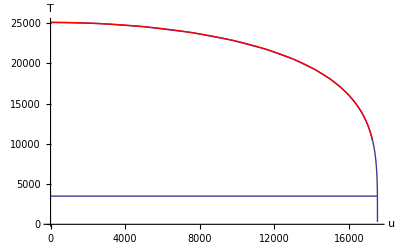

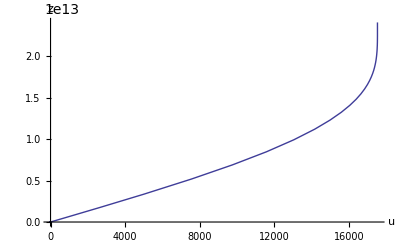

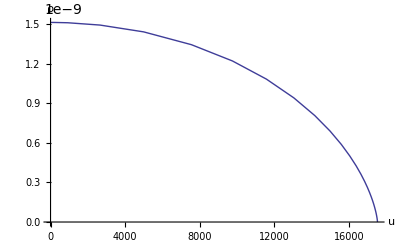

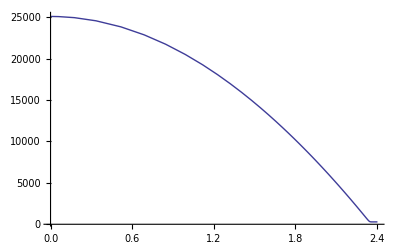

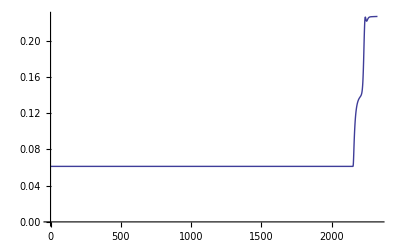

```mathematica
(*Example of a particular profile*)
M=10^7 Msun;
μe=1;
μ0=0.615;
κes=0.4 μe;
(*Import profile and extract physical parameters*)
MyFile="profile-35035-0.1-1000";
MyFileP=StringSplit[MyFile, "-"]//#[[2;;]]&;
MyFileP=ToExpression/@MyFileP;
Σ=MyFileP[[1]];
Ṁ=MyFileP[[2]] 10 4 π G M/(c κes);
R=MyFileP[[3]] 2 G M/c^2;
(*Kinematic viscosity*)
ν=(Ṁ)/(3π Σ);
(*Keplerian angular velocity*)
Ω=√(G M/R^3);
(*Central sound speed*)
cs0=√(kb Tc/(μ0 mp))

Teff=((9/8 ν Σ)Ω^2/σ)^0.25;
Tss[Tc_, u_, Σ_]:=Tc(1-4(u/Σ)^2)^(1/4);
(*Finding the points which bracket the effective temperature*)
tlow=(Position[profile[[All, 4]], x_/;x<Teff])[[1]];
thigh=(Position[profile[[All, 4]], x_/;x>Teff])[[-1]];
Extract[profile[[All,1]],{thigh, tlow}]
Print["u^*=",Σ/2 √(1-8/((3/2)κes Σ))]

profile=Import[NotebookDirectory[]<>MyFile,"Table"];
u0=profile[[All,1]]//Min;
umax=profile[[All,1]]//Max;
Tc=profile[[1,4]];
t1=Show[{profile[[All,{1,4}]]}//ListLinePlot[#, PlotRange->All]&,Plot[Teff,{u,u0,umax}],PlotRange->All,AxesLabel->{"u","T"},AxesOrigin->{0,0}];
t2=Plot[Tss[Tc, u, Σ], {u,0, umax}, PlotStyle->Directive[Red]];
Show[t1, t2]
{profile[[All,{1,2}]]}//ListLinePlot[#,AxesLabel->{"u","z"}, PlotRange->All]&
{profile[[All,{1,3}]]}//ListLinePlot[#,AxesLabel->{"u","ρ"}, PlotRange->All]&
profile[[All,{2,4}]]//ListLinePlot[#,PlotRange->All,AxesOrigin->{0,0}, PlotRange->All]&
(profile[[All,6]]-profile[[All,7]])//ListLinePlot[#, AxesOrigin->{0, 0}]&
```

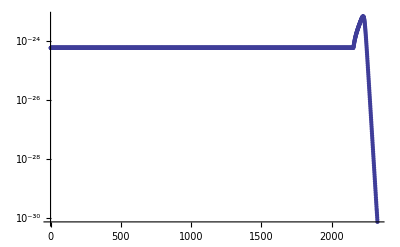

```mathematica
profile[[All, 3]]  profile[[All, 4]]^(-7/2)//ListLogPlot
```